(6 (400-40 x+x^2-y^2))/((400-40 x+x^2+y^2)^2)

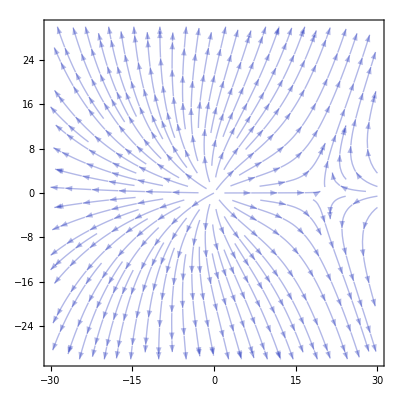

-Graphics3D-

```mathematica
{u,v}=(5 {x,y})/(x^2+y^2)+(3 {20-x,y})/((20-x)^2+y^2);

fn={u,v};

div=Simplify[Div[fn,{x,y}]]

start=-30;end=-start;len=end;
StreamPlot[fn,{x,start,end},{y,start,end},StreamStyle->{Opacity[0.3]}]
Plot3D[div,{x,start,end},{y,start,end},PlotLegends->Automatic]
```

```mathematica
(6 (400-40 x+x^2-y^2))/((400-40 x+x^2)
```

```mathematica
(*二维电场强度 大小跟 1/r 成正比，非零点散度处处为零*)
fnE={u, v}=(5 {x,y})/(x^2+y^2); (*= (5 {x,y})/(x^2+y^2)+(3 {20-x,y})/((20-x)^2+y^2)*)
divE1= Simplify[Div[fnE,{x,y}]]
divE2=Simplify[D[u,x]+D[v,y]]
```

0

0

```mathematica
(*三维电场强度 大小跟1/r^2成正比 散度是0 但是他在0点有散度*)
fnE={u, v, w} = {x,y,z}/((x^2+y^2+z^2)^(3/2))+(4*{x-20,y,z})/(((（20-x）)^2+y^2+z^2)^(3/2));
Simplify[Div[fnE,{x,y,z}]]
Simplify[D[u,x]+D[v,y]+D[w,z]]
```

0

0